-6.14724+0.000500917 x

-0.0288546+7.55172×10^-6 x+3.03448×10^-9 x^2

-0.0998419+0.000020404 x+2.84002×10^-9 x^2+6.79964×10^-16 x^3

-0.0214544-9.91421×10^-7 x+3.44382×10^-9 x^2-4.55857×10^-15 x^3+1.37689×10^-20 x^4

0.139882-0.000148344 x+2.83418×10^-8 x^2-1.5772×10^-12 x^3+4.54088×10^-17 x^4-6.70478×10^-22 x^5+5.24334×10^-27 x^6-2.05962×10^-32 x^7+3.18722×10^-38 x^8

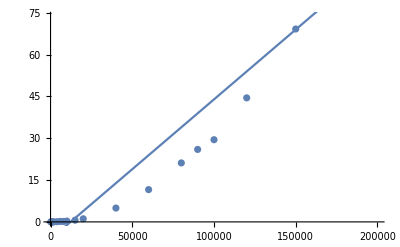

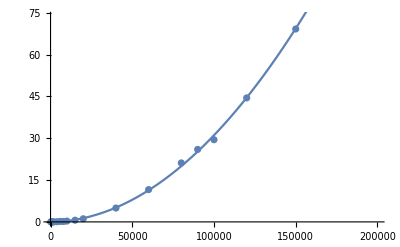

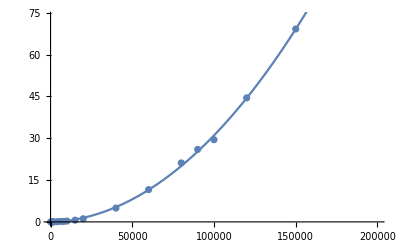

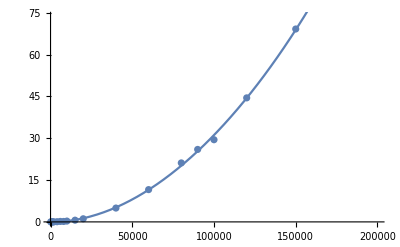

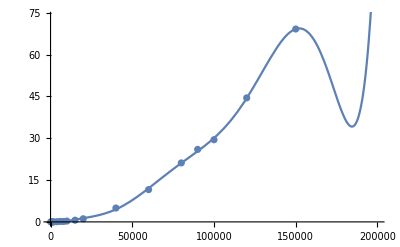

```mathematica
BSO1=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x},x]

BSO2=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2},x]

BSO3=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3},x]

BSO4=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3,x^4},x]

BSO8=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}}]

g1=Plot[BSO1,{x,0,200000}]
Show[puntos,g1]

g2=Plot[BSO2,{x,0,200000}]
Show[puntos,g2]

g3=Plot[BSO3,{x,0,200000}]
Show[puntos,g3]

g4=Plot[BSO4,{x,0,200000}]
Show[puntos,g4]

g8=Plot[BSO8,{x,0,200000}]
Show[puntos,g8]
```